```mathematica
Clear["Global`*"]
```

## Classical thermal gas in harmonic trap

See David Tong’s lecture notes on statistical mechanics (http://www.damtp.cam.ac.uk/user/tong/statphys.html).

```mathematica
V[x_,y_,z_]:=1/2 m(ωx^2 x^2+ωy^2 y^2+ωz^2 z^2);
ϵ[x_,y_,z_,px_,py_,pz_]:=1/(2m)(px^2+py^2+pz^2)+V[x,y,z];
```

### Partition function

```mathematica
FullSimplify[1/h^3 Integrate[Exp[-β ϵ[x,y,z,px,py,pz]],{px,-Infinity,Infinity},{py,-Infinity,Infinity},{pz,-Infinity,Infinity},{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}],{β>0,m>0,ωx>0,ωy>0,ωz>0}]
```

(8 π^3)/(h^3 β^3 ωx ωy ωz)

```mathematica
FullSimplify[1/h^3 Integrate[Exp[-β 1/(2m)(px^2+py^2+pz^2)],{px,-Infinity,Infinity},{py,-Infinity,Infinity},{pz,-Infinity,Infinity}],{β>0,m>0,ωx>0,ωy>0,ωz>0}]
```

(2 √2 π^(3/2) (m/β)^(3/2))/h^3

## Ellipsoidal (x,y,z) to spherical (x,y,z)=(r,θ,ϕ)

```mathematica
1/2 m Expand[(ωx^2 x^2+ωy^2 y^2+ωz^2 z^2)]
```

1/2 m (x^2 ωx^2+y^2 ωy^2+z^2 ωz^2)

## Thermal density

Working with x’, y’, z’.

```mathematica
V[x_,y_,z_]:=1/2 m (x^2 ωx^2+y^2 ωy^2+z^2 ωz^2);
ϵ[x_,y_,z_,vx_,vy_,vz_]:=1/2 m(vx^2+vy^2+vz^2)+V[x,y,z];
```

```mathematica
(*Partition function*)
FullSimplify[Integrate[Exp[-β ϵ[x,y,z,vx, vy,vz]],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity},{vx,-Infinity,Infinity},{vy,-Infinity,Infinity},{vz,-Infinity,Infinity}],{m>0,β>0,ωx>0,ωy>0,ωz>0}]
```

(8 π^3)/(m^3 β^3 ωx ωy ωz)

```mathematica
(*Boltzmann distribution, integrating over velocities*)
FullSimplify[Assuming[{m>0,β>0,ωx>0,ωy>0,ωz>0},Integrate[((8 π^3)/(m^3 β^3 ωx ωy ωz))^-1 Exp[-β ϵ[x,y,z,vx, vy,vz]],{vx,-Infinity,Infinity},{vy,-Infinity,Infinity},{vz,-Infinity,Infinity}]]]
```

(ⅇ^(-1/2 m β (x^2 ωx^2+y^2 ωy^2+z^2 ωz^2)) (m β)^(3/2) ωx ωy ωz)/(2 √2 π^(3/2))

```mathematica
(*Testing below*)
```

```mathematica
(ⅇ^(-1/2 m β (x^2 ωx^2+y^2 ωy^2+z^2 ωz^2)) (m β)^(3/2) ωx ωy ωz)/(2 √2 π^(3/2))((m β)/(2π))^(-3/2)
```

ⅇ^(-1/2 m β (x^2 ωx^2+y^2 ωy^2+z^2 ωz^2)) ωx ωy ωz

```mathematica
(ⅇ^(-1/2 m  r^2 β ωx^2 ωy^2 ωz^2) (m β)^(3/2) ωx^3 ωy^3 ωz^3)/(2 √2 π^(3/2))/.r->0
```

((m β)^(3/2) ωx^3 ωy^3 ωz^3)/(2 √2 π^(3/2))

```mathematica
ρ0==((m β)^(3/2) ωx^3 ωy^3 ωz^3)/(2 √2 π^(3/2));
```

```mathematica
FullSimplify[(((m β)^(3/2) ωx^3 ωy^3 ωz^3)/(2 √2 π^(3/2)))^-1((ⅇ^(-1/2 m  r^2 β ωx^2 ωy^2 ωz^2) (m β)^(3/2) ωx^3 ωy^3 ωz^3)/(2 √2 π^(3/2)))]
```

ⅇ^(-1/2 m r^2 β ωx^2 ωy^2 ωz^2)

```mathematica
Solve[ρ==ⅇ^(-1/2 m r^2 β ωx^2 ωy^2 ωz^2),r]
```

```mathematica
FullSimplify[Log[ⅇ^(-1/2 m r^2 β ωx^2 ωy^2 ωz^2)]-(-1/2 m r^2 β ωx^2 ωy^2 ωz^2),{r>0,β>0,ωx>0,ωy>0,ωz>0}]
```

1/2 m r^2 β ωx^2 ωy^2 ωz^2+Log[ⅇ^(-1/2 m r^2 β ωx^2 ωy^2 ωz^2)]

```mathematica
FullSimplify[Solve[-Log[ρ0/ρ]==-1/2 m r^2 β ωx^2 ωy^2 ωz^2,r],{ρ>0,ρ0>0,m>0,β>0,ωx>0,ωy>0,ωz>0}]
```

{{r→-(√2 √Log[ρ0/ρ])/(√(m β) ωx ωy ωz)},{r→(√2 √Log[ρ0/ρ])/(√(m β) ωx ωy ωz)}}

```mathematica
(*Now that we have r(ρ)..., transform N=4π Int[r^2 ρ(r) dr] = Int[g(ρ) dρ]*)
```

```mathematica
dr/dρ==D[(√2 √Log[ρ0/ρ])/(√(m β) ωx ωy ωz),ρ]
```

dr/dρ==-1/(√2 √(m β) ρ ωx ωy ωz √Log[ρ0/ρ])

```mathematica
FullSimplify[4π ((√2 √Log[ρ0/ρ])/(√(m β) ωx ωy ωz))^2 1/(√2 √(m β) ρ ωx ωy ωz √Log[ρ0/ρ])dρ ρ]
```

(4 √2 dρ π √Log[ρ0/ρ])/((m β)^(3/2) ωx^3 ωy^3 ωz^3)

```mathematica
f(ρ)==1/ρ(4 √2 π √Log[ρ0/ρ])/((m β)^(3/2) ωx^3 ωy^3 ωz^3)
1/ρ(4 √2 π √Log[ρ0/ρ])/((m β)^(3/2) ωx^3 ωy^3 ωz^3)/.{ωx->1,ωy->1,ωz->1,m->1,β->0.001,ρ0->1}
```

f ρ==(4 √2 π √Log[ρ0/ρ])/((m β)^(3/2) ρ ωx^3 ωy^3 ωz^3)

(561985. √Log[1/ρ])/ρ

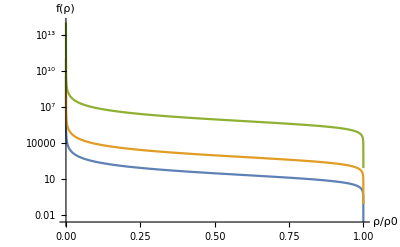

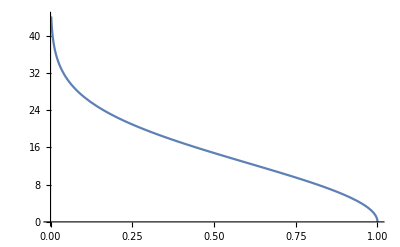

```mathematica
LogPlot[{(4 √2 π √Log[1/ρ])/ρ,(561.985178483258 √Log[1/ρ])/ρ,(561985.1784832582 √Log[1/ρ])/ρ},{ρ,0,1},AxesLabel->{"ρ/ρ0","f(ρ)"}]
Plot[{4 √2 π √Log[1/ρ]},{ρ,0,1}]
```